```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
NN=200;
z=RandomReal[{0,20},NN];
Things=RandomReal[{0,1},{NN,5}];
U=Table[Graphics3D[{Opacity[0.03Things[[ii,1]]],Blend[{Cyan,Gray},Things[[ii,2]]],Ellipsoid[{8+4Things[[ii,1]]Sin[2π Things[[ii,2]]],8+4Things[[ii,1]]Cos[2π Things[[ii,2]]],z[[ii]]},{3+0.5(Things[[ii,3]]-0.5),3+0.5(Things[[ii,4]]-0.5),3+0.5(Things[[ii,5]]-0.5)}]}],{ii,1,NN}];
```

```mathematica
Arrow1=Graphics3D[{Lighter@Darker[Red,0.2] ,Arrowheads[0.08],Arrow[Tube[{{0+8,0+8,-7},{0+8,0+8,22}},0.2]]}];
Show[U,Arrow1,Lighting->"Neutral",ImageSize->Large,PlotRange->All,Boxed->False]
```

-Graphics3D-

```mathematica
A=Import["thing0.csv"];
```

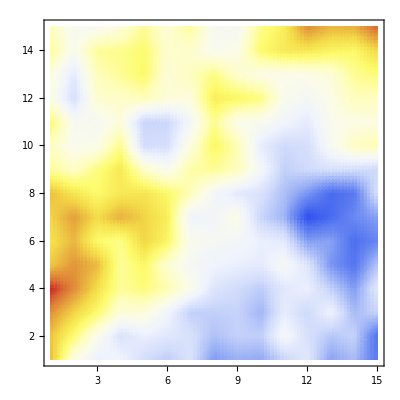

```mathematica
ListDensityPlot[A,InterpolationOrder->1,ColorFunction->ColorData["TemperatureMap"]]
```

```mathematica
CuteBlue=RGBColor[0,90/255,181/155]; 
CuteRed=RGBColor[220/255,50/255,32/155];
```

{{0.10425,0.0187563,-0.0110359,-0.00511684,-0.0309474,-0.0432617,-0.0242174,-0.0744245,-0.0617146,-0.0658881,-0.0373814,-0.0190853,-0.0701562,-0.0539632,-0.0998208},{0.0995464,0.0627987,0.0143679,-0.0262012,-0.012142,-0.0202215,-0.0268506,-0.0506966,-0.0395852,-0.041185,0.00252509,-0.0275433,-0.0467905,-0.0383428,-0.104178},{0.123503,0.091732,0.0651227,0.0245896,0.0237011,-0.00344781,-0.0409738,-0.0406303,-0.0383282,-0.0578961,-0.0152691,-0.0342895,-0.00677157,-0.0548884,-0.036843},{0.160422,0.125439,0.0861849,0.0500297,0.059592,0.0429375,0.0153487,-0.0228434,-0.0320074,-0.0429205,-0.0191593,-0.0116328,-0.0401919,-0.0741797,-0.017308},{0.0964462,0.120896,0.104229,0.0490171,0.067879,0.0280229,0.00222443,-0.00715193,-0.0119185,-0.0161629,0.0036721,-0.0214958,-0.0779591,-0.102168,-0.0476932},{0.0833357,0.105148,0.0643019,0.0548423,0.0911686,0.0689844,0.0105858,0.0026006,-0.000494346,-0.0112721,-0.0178645,-0.0731634,-0.0698402,-0.106815,-0.088934},{0.0904698,0.116177,0.087816,0.108447,0.0923171,0.0752994,-0.00637194,-0.00240621,0.0158497,-0.0364129,-0.0587073,-0.129263,-0.109834,-0.087073,-0.0709478},{0.101667,0.0809882,0.0644537,0.0787415,0.082014,0.0658589,0.0396023,0.,-0.0182452,-0.0257154,-0.0518438,-0.0777282,-0.108858,-0.0990173,-0.0246825},{0.0496546,0.0325104,0.0578542,0.0797408,0.0337111,0.0105515,0.0460528,0.0507707,0.0381298,0.00138596,-0.0404337,-0.0328871,-0.0269772,-0.0296614,-0.0340771},{0.0354458,0.0108779,0.0141699,0.0550739,-0.0307477,-0.0292502,0.0201765,0.0683053,0.0417755,-0.0148691,-0.0336163,-0.0294757,0.0065788,0.0355724,0.0421621},{0.0629571,0.00869454,0.00457786,0.0232363,-0.036499,-0.0356296,-0.000708352,0.053469,0.0134919,0.00979257,-0.00444653,-0.0168212,0.0118494,0.0168516,0.0192679},{0.0170041,-0.0295137,0.0281037,0.0314937,0.0390046,0.0239996,0.0215694,0.0750567,0.0677801,0.058089,0.0111864,0.00103155,0.0165714,0.0375299,0.0372965},{0.0219962,-0.0180111,0.0380936,0.0513485,0.0657711,0.0249603,0.0364384,0.0561485,0.0302827,0.0157453,0.0137881,0.0162106,0.0236343,0.0509928,0.0603334},{0.050787,0.00973636,0.0509093,0.0532768,0.0639972,0.0298055,0.0300951,0.0100798,0.0152057,0.0633992,0.0784757,0.0785133,0.0696185,0.0662635,0.0891885},{0.037348,0.00718086,0.00653203,0.0231279,0.0502108,0.0245496,0.0500664,0.00718604,0.00335768,0.0544564,0.0748352,0.124558,0.106325,0.108087,0.142066}}

-Graphics3D-

```mathematica
Arrow1=Graphics3D[{Lighter@Darker[Gray,0.2] ,Arrowheads[0.08],Arrow[Tube[{{0+8,0+8,-12},{0+8,0+8,38}},0.4]]}];

A=Import["thing0.csv"];
Plane1=ListPlot3D[0A-10,PlotStyle->Darker[Gray,0.95],RegionFunction->Function[{x,y},Sqrt[(x-8)^2+(y-8)^2]≤ 7],Lighting->"Neutral",Mesh->None];

A1=Import["thing100.csv"];
Plane2=ListPlot3D[5A1+30,ColorFunction->(Blend[{CuteBlue,Gray,CuteRed},#3]&),RegionFunction->Function[{x,y},Sqrt[(x-8)^2+(y-8)^2]≤ 7],InterpolationOrder->2,Lighting->"Neutral",Mesh->None];

Show[Arrow1,U,Plane1,Plane2,PlotRange->All,Boxed->False,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
A=Import["thing0.csv"];
Plane1=ListPlot3D[0A-10,PlotStyle->Darker@Gray,RegionFunction->Function[{x,y},Sqrt[(x-8)^2+(y-8)^2]≤ 7],Lighting->"Neutral",Mesh->None]
```

-Graphics3D-

```mathematica
A1=Import["thing100.csv"];
Plane2=ListPlot3D[A1/0.633,ColorFunction->ColorData["Rainbow"],
RegionFunction->Function[{x,y},Sqrt[(x-8)^2+(y-8)^2]≤ 7],
PlotRange->{{-1,16},{-1,16},{-0.5,0.5}},
InterpolationOrder->2,
Lighting->"Neutral",
Boxed->{Back,Bottom,Left},
BoxStyle->Directive[Black,Thick],
Ticks->{{{0,-2},{7.5,0},{15,2}},{{0,-2},{7.5,0},{15,2}},Automatic},
FaceGrids->{{{0,1,0},{{{0,Directive[Thick,Dashed]},{7.5,Directive[Thick,Dashed]},{15,Directive[Thick,Dashed]}},{{-0.25,Directive[Thick,Dashed]},{0.25,Directive[Thick,Dashed]},{0,Directive[Thick,Dashed]}}}},{{0,0,-1},{{{0,Directive[Thick,Dashed]},{7.5,Directive[Thick,Dashed]},{15,Directive[Thick,Dashed]}},{{0,Directive[Thick,Dashed]},{7.5,Directive[Thick,Dashed]},{15,Directive[Thick,Dashed]}}}},{{-1,0,0},{{{0,Directive[Thick,Dashed]},{7.5,Directive[Thick,Dashed]},{15,Directive[Thick,Dashed]}},{{-0.25,Directive[Thick,Dashed]},{0.25,Directive[Thick,Dashed]},{0,Directive[Thick,Dashed]}}}}},
TicksStyle->Directive[Black,FontFamily->"Arial",FontSize->30],
BoxRatios->{1, 1,3/5 },ImageSize->Large,AxesLabel->{"x/w_0","y/w_0","z/λ"},Axes->True,AxesStyle->Directive[Black,FontFamily->"Arial",FontSize->30]]
```

-Graphics3D-

```mathematica
t
FaceGridsStyle->Directive[Gray,Dashed,Thick],
```

```mathematica
Graphics3D[Cylinder[],FaceGrids->{{{0,-1,0},{{{-1/2,Red},{0,Green},{1/2,Blue},{-1/3,Green}}}}}]
```

-Graphics3D-

```mathematica
Plane2
```

-Graphics3D-

```mathematica
Dimensions[A1]
```

{15,15}

```mathematica
Graphics3D[Cylinder[],]
```